```mathematica
r[t_]:={
-10 t^3+9 t^2+1,
10 t^3-21 t^2+12t
}
p[λ_]:=r[3/(4 √5)λ];
λ0=(4 √5)/9;
D[p[λ],{λ,2}]/.λ->λ0//FullSimplify
```

{-9/40,-99/40}

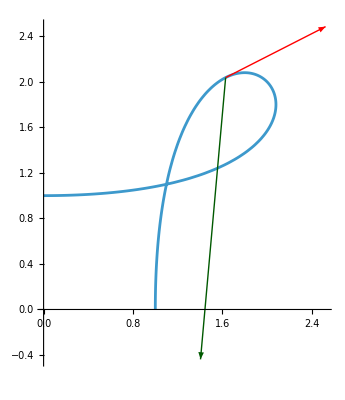

```mathematica
Show[
ParametricPlot[p[t],{t,0,(4 √5)/3}],
Graphics[{
Red,
Arrow[{p[λ0],p[λ0]+D[p[λ],{λ,1}]/.λ->λ0}],
DarkGreen,
Arrow[{p[λ0],p[λ0]+D[p[λ],{λ,2}]/.λ->λ0}]
}],
PlotRange->All
]
```

```mathematica
D[r[t],t]/.t->1/3//FullSimplify
```

{8/3,4/3}

```mathematica
ArcCurvature[r[t],t]/.t->1/3
```

```mathematica
189/(40 √5)
```

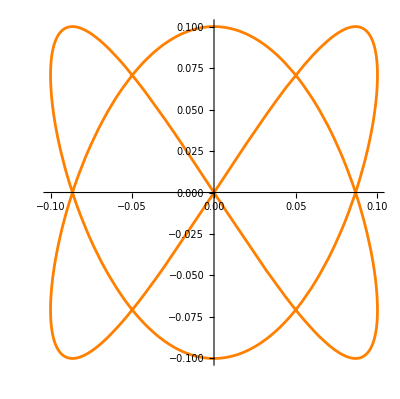

```mathematica
Parametri.b4cPlot[0.1{Sin[2θ],Cos[3θ]},{θ,0,2π},PlotStyle->Orange]
```

```mathematica
p[t_]:={-t,1-t^2}
T[t_]:=Normalize[D[p[s],s]]/.s->t
No[t_]:={{0,-1},{1,0}}.T[t]
Animate[
Show[
ParametricPlot[p[t],{t,-1,1}],
Graphics[{
Red,
Arrow[{p[s],p[s]+T[s]}],
Blue,
Arrow[{p[s],p[s]+No[s]}]
}],
ParametricPlot[p[s] + 0.1(Sin[2θ]*No[s]+Cos[3θ]*T[s]),{θ,0,2π},PlotStyle->Orange],
PlotRange->All
],
{{s,-0.45},-1,1}
]
```